```mathematica
ClearAll["Global`*"]
```

```mathematica
SetOptions[EvaluationNotebook[],Background->White]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/D"];
```

```mathematica
data=Import[#,"Table"]&/@FileNames["eval*"];
```

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
```

```mathematica
Do[ReEv[i]=Table[vec[i][[j,1]],{j,1,Length[vec[i]]}],{i,1,Length[data]}]
```

```mathematica
Do[MaxEv[i]=Max[ReEv[i]],{i,1,Length[data]}]
```

```mathematica
xs=Table[i*2/100,{i,1,Length[data]}];
ys=Table[2^(3/2)MaxEv[i],{i,1,Length[data]}];
pairs=Thread[{xs,ys}];
```

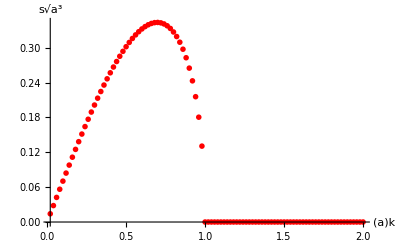

```mathematica
l1=ListPlot[pairs,PlotRange->All,Joined->False,PlotStyle->{PointSize[0.01],Red},AxesLabel->{"(a)k","s√(a^3)"},LabelStyle->Directive[14]]
```

```mathematica
s2[k_]:=Sqrt[1/2^3 2.*k*BesselI[1,2*k]/BesselI[0,2*k](1-(2*k)^2)]
```

```mathematica
xs2=Table[2*k,{k,.01,1,.01}];
ys2=Table[Re[s2[k]] 2^(3/2),{k,.01,1,.01}];
pairs2=Thread[{xs2,ys2}];
```

```mathematica
l3=ListPlot[pairs2,PlotRange->All,PlotStyle->Black,Joined->True,AxesLabel->{"(a)k","s√(a^3)"},LabelStyle->Directive[14]];
```

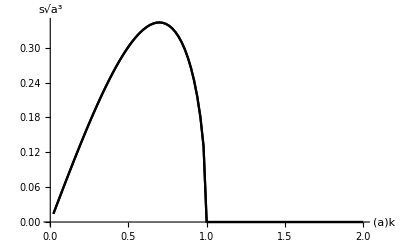

```mathematica
Show[l2,l3]
```

```mathematica
pairs3=Table[pairs2[[i]],{i,1,Length[pairs2],4}];
```

```mathematica
output=Flatten[{{{"ColumnX","ColumnY"}},pairs3},1];
```

```mathematica
SetDirectory["~/Documents/University of Illinois/Research/prelim_2016/D"];
```

```mathematica
Export["Inviscid_Num.csv",output,"Table"];
```

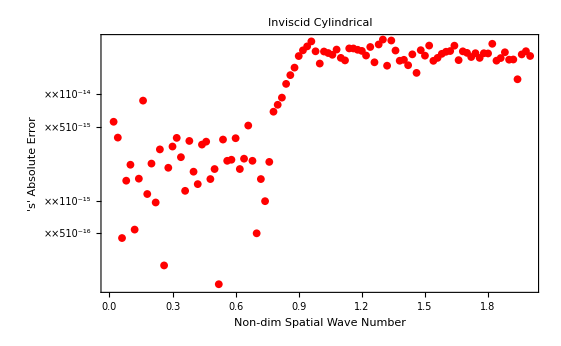

```mathematica
ListLogPlot[Table[{i*2/100,Abs[ys[[i]]-ys2[[i]]]},{i,1,100}],Frame->True,FrameLabel->{"Non-dim Spatial Wave Number","'s' Absolute Error"},LabelStyle->{FontFamily->"Helvetica",Directive[14]},PlotStyle->{Red,PointSize[0.01]},PlotLabel->"Inviscid Cylindrical"]
```